# Vacuum Decay Rate

## Effective Potential in 1d

Plug in the vev condition for S and eliminate it.

```mathematica
ClearAll["Global`*"]
g=0.65;
gY=0.36;
yt=0.9945;
Q=150;
mh=125.;
μH2[mS_,sinθ_]:=(mh^2 mS^2)/(2(sinθ^2 mh^2+(1-sinθ^2)mS^2));
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
S[A_,μS_,h_]:=A/(2 μS^2)h^2;
V0[λ_,A_,μH_,μS_,h_]:=1/4 λ h^4-1/2 μH^2 h^2+1/2 μS^2 S[A,μS,h]^2-1/2 A S[A,μS,h] h^2;
mW[h_]:=1/4 g^2 h^2;
mZ[h_]:=1/4(g^2+gY^2)h^2;
mt[h_]:=1/2 yt^2 h^2;
mX[λ_,A_,μH_,μS_,h_]:=-μH^2-A S[A,μS,h]+λ h^2;
sqrt[λ_,A_,μH_,μS_,h_]:=√(A^2(4 h^2+ S[A,μS,h]^2)+2A S[A,μS,h](μH^2+μS^2-3λ h^2)+(μH^2+μS^2-3λ h^2)^2);
mH[λ_,A_,μH_,μS_,h_]:=1/2(-μH^2+μS^2-A S[A,μS,h]+3λ h^2+sqrt[λ,A,μH,μS,h]);
mS[λ_,A_,μH_,μS_,h_]:=1/2(-μH^2+μS^2-A S[A,μS,h]+3λ h^2-sqrt[λ,A,μH,μS,h]);
VCW[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5/6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5/6)+mH[λ,A,μH,μS,h]^2(Log[Abs[mH[λ,A,μH,μS,h]]/Q^2]-3/2)+3 mX[λ,A,μH,μS,h]^2(Log[Abs[mX[λ,A,μH,μS,h]]/Q^2]-3/2)-12 mt[h]^2(Log[mt[h]/Q^2]-3/2));
V0T[λ_,A_,μH_,μS_,h_]:=V0[λ,A,μH,μS,h]+VCW[λ,A,μH,μS,h]-(V0[λ,A,μH,μS,10^-3]+VCW[λ,A,μH,μS,10^-3]);
```

```mathematica
fitting=Table[{ϕ,V0T[0.125299,10.6204,20.2598,21.8138,ϕ]},{ϕ,10^-3,10000,1}];
```

86.6867

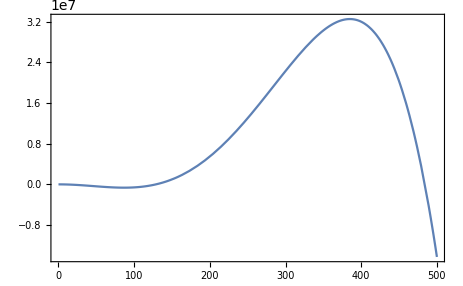

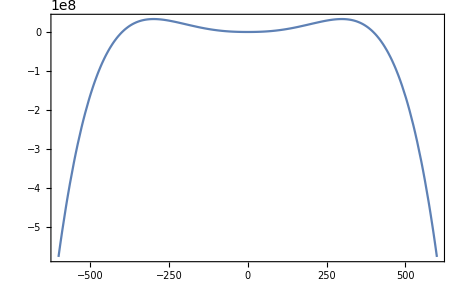

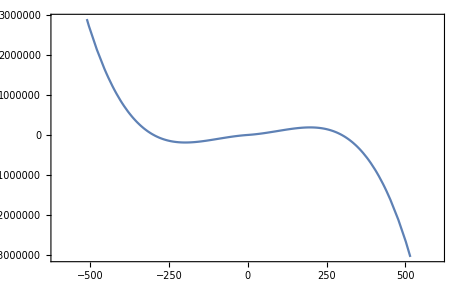

```mathematica
Vfit[ϕ_]=Interpolation[fitting][ϕ];
vev=ϕ/.FindMinimum[Vfit[ϕ],{ϕ,100}][[2]]
Vb[ϕ_]:=Vfit[ϕ+vev]/;ϕ≥0;
Vb[ϕ_]:=Vfit[-ϕ+vev]/;ϕ<0;
dVfit[ϕ_]:=Vfit'[ϕ+vev]/;ϕ≥0;
dVfit[ϕ_]:=-Vfit'[-ϕ+vev]/;ϕ<0;
Plot[Vfit[ϕ],{ϕ,0,500}]
Plot[Vb[ϕ],{ϕ,-600,600}]
Plot[dVfit[ϕ],{ϕ,-600,600}]
```

```mathematica
FindMaximum[Vb[ϕ],{ϕ,400}]
```

{3.25011×10^7,{ϕ→298.26}}

```mathematica
FindMinimum[Vb[ϕ],{ϕ,100}]
```

{-648783.,{ϕ→-2.37025×10^-7}}

```mathematica
ϕIR=10^-3;
rIR=10^-3;
ranger=0.2;
shootinginitial=400;
shootingfinal=5400;
δϕ0=10^3;
δϕ1=10^2;
δϕ2=10^1;
δϕ3=10^0;
δϕ4=10^-1;
δϕ5=10^-2;
δϕ6=10^-3;
δr=0.02*ranger;
```

```mathematica
overshoot‵trigger[escape0_]:=Catch[Do[If[NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[rIR]==escape0
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t]<0,Throw[t]],{t,rIR,ranger,δr}]]
```

```mathematica
overshoot‵trigger[4600]
```

0.033

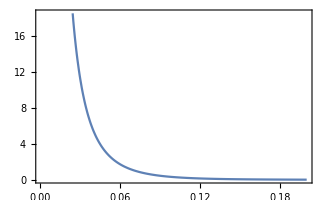

```mathematica
try[t_]=NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[ϕIR]==initial66
,ϕ'[ϕIR]==0},ϕ,{r,rIR,ranger}][t];
Plot[try[t],{t,rIR,0.2}]
```

```mathematica
initial00=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,shootinginitial,shootingfinal,δϕ0}]];
initial11=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial00-δϕ0,shootingfinal,δϕ1}]];
initial22=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial11-δϕ1,shootingfinal,δϕ2}]];
initial33=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial22-δϕ2,shootingfinal,δϕ3}]];
initial44=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial33-δϕ3,shootingfinal,δϕ4}]];
initial55=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial44-δϕ4,shootingfinal,δϕ5}]];
initial66=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial55-δϕ5,shootingfinal,δϕ6}]]
```

913623/200

```mathematica
initial66//N
```

4568.12

```mathematica
rinfty[initialf_]:=Catch[Do[If[NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[rIR]==initialf
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t]<0,Throw[t]],{t,rIR,ranger,δr}]];
bounceaction[initial_,rinf_]:=NIntegrate[Evaluate[4π r^2(1/2 ϕ'[r]*ϕ'[r]+Vb[ϕ[r]])/.NDSolve[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[rIR]==initial
,ϕ'[rIR]==0},ϕ,{r,rIR,rinf}]],{r,rIR,rinf}]
rinfty[initial66]
```

0.193

```mathematica
bounceaction[initial66,rinfty[initial66]]
```

{17436.5}